# Bistable motif: 2kinase1substrate

## Finding the condition of multistationarity

We consider the following reactions:

K+S→KS→K+S_p
K_p+S→K_p S→K_p+S_p
K→K_p
KS←K_p S
E+S→ES→E+S_p
E_p+S→E_p S→E_p+S_p
E→E_p
ES←E_p S
S_p→S

The species of the system are:

{S,S_p,K,K_p,KS,K_p S,E,E_p,ES,E_p S}

In total, there are 13 reations and 10 species.

We firstly construct the ordinary differential equations based on mass-action kinetics. Then compute the determinant of Jacobian, using the solution at critical point (steady state) to calculate the determinant. The (necessary) condition for multistationarity is to make determinant equal to zero (non-zero determinant implys injectivity).

```mathematica
A=Table[0,{13},{10}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;
A[[2]][[3]]=1;A[[2]][[2]]=1;A[[2]][[5]]=-1;
A[[3]][[1]]=-1;A[[3]][[4]]=-1;A[[3]][[6]]=1;
A[[4]][[4]]=1;A[[4]][[2]]=1;A[[4]][[6]]=-1;
A[[5]][[3]]=-1;A[[5]][[4]]=1;A[[6]][[5]]=1;A[[6]][[6]]=-1;
A[[13]][[2]]=-1;A[[13]][[1]]=1;
A[[7]][[1]]=-1;A[[7]][[7]]=-1;A[[7]][[9]]=1;
A[[8]][[7]]=1;A[[8]][[2]]=1;A[[8]][[9]]=-1;
A[[9]][[1]]=-1;A[[9]][[8]]=-1;A[[9]][[10]]=1;
A[[10]][[8]]=1;A[[10]][[2]]=1;A[[10]][[10]]=-1;
A[[11]][[7]]=-1;A[[11]][[8]]=1;
A[[12]][[9]]=1;A[[12]][[10]]=-1;
```

```mathematica
stoiM=Transpose[A]
```

{{-1,0,-1,0,0,0,-1,0,-1,0,0,0,1},{0,1,0,1,0,0,0,1,0,1,0,0,-1},{-1,1,0,0,-1,0,0,0,0,0,0,0,0},{0,0,-1,1,1,0,0,0,0,0,0,0,0},{1,-1,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,-1,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,-1,0,0},{0,0,0,0,0,0,0,0,-1,1,1,0,0},{0,0,0,0,0,0,1,-1,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,-1,0,-1,0}}

```mathematica
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 4]×Subscript[x, 6],Subscript[k, 5]×Subscript[x, 3],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 7]×Subscript[x, 1],Subscript[k, 8]×Subscript[x, 9],Subscript[k, 9]×Subscript[x, 8]*Subscript[x, 1],Subscript[k, 10]*Subscript[x, 10],Subscript[k, 11]*Subscript[x, 7],Subscript[k, 12]×Subscript[x, 10],Subscript[k, 13]*Subscript[x, 2]}
```

{k_1 x_1 x_3,k_2 x_5,k_3 x_1 x_4,k_4 x_6,k_5 x_3,k_6 x_6,k_7 x_1 x_7,k_8 x_9,k_9 x_1 x_8,k_10 x_10,k_11 x_7,k_12 x_10,k_13 x_2}

```mathematica
ssEqns=stoiM.ks
```

{k_13 x_2-k_1 x_1 x_3-k_3 x_1 x_4-k_7 x_1 x_7-k_9 x_1 x_8,-k_13 x_2+k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10,-k_5 x_3-k_1 x_1 x_3+k_2 x_5,k_5 x_3-k_3 x_1 x_4+k_4 x_6,k_1 x_1 x_3-k_2 x_5+k_6 x_6,k_3 x_1 x_4-k_4 x_6-k_6 x_6,-k_11 x_7-k_7 x_1 x_7+k_8 x_9,k_11 x_7-k_9 x_1 x_8+k_10 x_10,k_7 x_1 x_7-k_8 x_9+k_12 x_10,k_9 x_1 x_8-k_10 x_10-k_12 x_10}

```mathematica
mC=RowReduce[NullSpace[A]]
```

{{1,1,0,0,1,1,0,0,1,1},{0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,1,1}}

```mathematica
cons={Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2],Subscript[x, 7]+Subscript[x, 8]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 3]};
```

```mathematica
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],ssEqns[[8]],ssEqns[[9]],cons[[1]],cons[[2]],cons[[3]]}
```

{-k_13 x_2+k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10,k_5 x_3-k_3 x_1 x_4+k_4 x_6,k_1 x_1 x_3-k_2 x_5+k_6 x_6,k_3 x_1 x_4-k_4 x_6-k_6 x_6,k_11 x_7-k_9 x_1 x_8+k_10 x_10,k_7 x_1 x_7-k_8 x_9+k_12 x_10,-T_1+x_1+x_2+x_5+x_6+x_9+x_10,-T_2+x_3+x_4+x_5+x_6,-T_3+x_7+x_8+x_9+x_10}

```mathematica
sol1=Solve[{ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],cons[[2]]}==0,{Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}]
```

{{x_3→(k_2 k_3 k_6 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_4→(k_2 k_5 (k_4+k_6) T_2)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_5→(k_3 T_2 (k_5 k_6 x_1+k_1 k_6 x_1^2))/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_6→(k_2 k_3 k_5 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)}}

```mathematica
sol2=Solve[{ssEqns[[8]],ssEqns[[9]],ssEqns[[10]],cons[[3]]}==0,{Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[x, 10]}]
```

{{x_7→(k_8 k_9 k_12 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_8→(k_8 k_11 (k_10+k_12) T_3)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_9→(k_9 T_3 (k_11 k_12 x_1+k_7 k_12 x_1^2))/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_10→(k_8 k_9 k_11 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2)}}

```mathematica
sol3=Subscript[x, 2]/.Solve[{ssEqns[[2]]==0},{Subscript[x, 2]}]
```

{(k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10)/k_13}

```mathematica
sol4=Solve[{Subscript[x, 2]==sol3[[1]]}/.Join[sol1[[1]],sol2[[1]]],{Subscript[x, 2]}]
```

{{x_2→1/k_13((k_2 k_3 k_4 k_5 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)+(k_2 k_3 T_2 (k_5 k_6 x_1+k_1 k_6 x_1^2))/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)+(k_8 k_9 k_10 k_11 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2)+(k_8 k_9 T_3 (k_11 k_12 x_1+k_7 k_12 x_1^2))/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2))}}

```mathematica
term=FullSimplify[Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 1]/.Join[sol1[[1]],sol2[[1]],sol4[[1]]]]
```

-T_1+(x_1 ((k_3 T_2 (k_5 (k_6 k_13+k_2 (k_4+k_6+k_13))+k_1 k_6 (k_2+k_13) x_1))/(k_3 k_6 x_1 (k_5+k_1 x_1)+k_2 (k_5 (k_4+k_6)+k_3 (k_5+k_6) x_1))+(k_9 k_12 k_13 (T_3+x_1) (k_11+k_7 x_1)+k_8 (k_11 ((k_10+k_12) k_13+k_9 (k_10+k_12+k_13) T_3)+k_9 ((k_11+k_12) k_13+k_7 k_12 T_3) x_1))/(k_9 k_12 x_1 (k_11+k_7 x_1)+k_8 (k_11 (k_10+k_12)+k_9 (k_11+k_12) x_1))))/k_13

```mathematica
polynomial=Collect[Numerator[Together[term]],Subscript[x, 1]]
```

-k_2 k_4 k_5 k_8 k_10 k_11 k_13 T_1-k_2 k_5 k_6 k_8 k_10 k_11 k_13 T_1-k_2 k_4 k_5 k_8 k_11 k_12 k_13 T_1-k_2 k_5 k_6 k_8 k_11 k_12 k_13 T_1+(k_2 k_4 k_5 k_8 k_10 k_11 k_13+k_2 k_5 k_6 k_8 k_10 k_11 k_13+k_2 k_4 k_5 k_8 k_11 k_12 k_13+k_2 k_5 k_6 k_8 k_11 k_12 k_13-k_2 k_4 k_5 k_8 k_9 k_11 k_13 T_1-k_2 k_5 k_6 k_8 k_9 k_11 k_13 T_1-k_2 k_3 k_5 k_8 k_10 k_11 k_13 T_1-k_2 k_3 k_6 k_8 k_10 k_11 k_13 T_1-k_3 k_5 k_6 k_8 k_10 k_11 k_13 T_1-k_2 k_4 k_5 k_8 k_9 k_12 k_13 T_1-k_2 k_5 k_6 k_8 k_9 k_12 k_13 T_1-k_2 k_3 k_5 k_8 k_11 k_12 k_13 T_1-k_2 k_3 k_6 k_8 k_11 k_12 k_13 T_1-k_3 k_5 k_6 k_8 k_11 k_12 k_13 T_1-k_2 k_4 k_5 k_9 k_11 k_12 k_13 T_1-k_2 k_5 k_6 k_9 k_11 k_12 k_13 T_1+k_2 k_3 k_4 k_5 k_8 k_10 k_11 T_2+k_2 k_3 k_5 k_6 k_8 k_10 k_11 T_2+k_2 k_3 k_4 k_5 k_8 k_11 k_12 T_2+k_2 k_3 k_5 k_6 k_8 k_11 k_12 T_2+k_2 k_3 k_5 k_8 k_10 k_11 k_13 T_2+k_3 k_5 k_6 k_8 k_10 k_11 k_13 T_2+k_2 k_3 k_5 k_8 k_11 k_12 k_13 T_2+k_3 k_5 k_6 k_8 k_11 k_12 k_13 T_2+k_2 k_4 k_5 k_8 k_9 k_10 k_11 T_3+k_2 k_5 k_6 k_8 k_9 k_10 k_11 T_3+k_2 k_4 k_5 k_8 k_9 k_11 k_12 T_3+k_2 k_5 k_6 k_8 k_9 k_11 k_12 T_3+k_2 k_4 k_5 k_8 k_9 k_11 k_13 T_3+k_2 k_5 k_6 k_8 k_9 k_11 k_13 T_3+k_2 k_4 k_5 k_9 k_11 k_12 k_13 T_3+k_2 k_5 k_6 k_9 k_11 k_12 k_13 T_3) x_1+(k_2 k_4 k_5 k_8 k_9 k_11 k_13+k_2 k_5 k_6 k_8 k_9 k_11 k_13+k_2 k_3 k_5 k_8 k_10 k_11 k_13+k_2 k_3 k_6 k_8 k_10 k_11 k_13+k_3 k_5 k_6 k_8 k_10 k_11 k_13+k_2 k_4 k_5 k_8 k_9 k_12 k_13+k_2 k_5 k_6 k_8 k_9 k_12 k_13+k_2 k_3 k_5 k_8 k_11 k_12 k_13+k_2 k_3 k_6 k_8 k_11 k_12 k_13+k_3 k_5 k_6 k_8 k_11 k_12 k_13+k_2 k_4 k_5 k_9 k_11 k_12 k_13+k_2 k_5 k_6 k_9 k_11 k_12 k_13-k_2 k_3 k_5 k_8 k_9 k_11 k_13 T_1-k_2 k_3 k_6 k_8 k_9 k_11 k_13 T_1-k_3 k_5 k_6 k_8 k_9 k_11 k_13 T_1-k_1 k_3 k_6 k_8 k_10 k_11 k_13 T_1-k_2 k_4 k_5 k_7 k_9 k_12 k_13 T_1-k_2 k_5 k_6 k_7 k_9 k_12 k_13 T_1-k_2 k_3 k_5 k_8 k_9 k_12 k_13 T_1-k_2 k_3 k_6 k_8 k_9 k_12 k_13 T_1-k_3 k_5 k_6 k_8 k_9 k_12 k_13 T_1-k_1 k_3 k_6 k_8 k_11 k_12 k_13 T_1-k_2 k_3 k_5 k_9 k_11 k_12 k_13 T_1-k_2 k_3 k_6 k_9 k_11 k_12 k_13 T_1-k_3 k_5 k_6 k_9 k_11 k_12 k_13 T_1+k_2 k_3 k_4 k_5 k_8 k_9 k_11 T_2+k_2 k_3 k_5 k_6 k_8 k_9 k_11 T_2+k_1 k_2 k_3 k_6 k_8 k_10 k_11 T_2+k_2 k_3 k_4 k_5 k_8 k_9 k_12 T_2+k_2 k_3 k_5 k_6 k_8 k_9 k_12 T_2+k_1 k_2 k_3 k_6 k_8 k_11 k_12 T_2+k_2 k_3 k_4 k_5 k_9 k_11 k_12 T_2+k_2 k_3 k_5 k_6 k_9 k_11 k_12 T_2+k_2 k_3 k_5 k_8 k_9 k_11 k_13 T_2+k_3 k_5 k_6 k_8 k_9 k_11 k_13 T_2+k_1 k_3 k_6 k_8 k_10 k_11 k_13 T_2+k_2 k_3 k_5 k_8 k_9 k_12 k_13 T_2+k_3 k_5 k_6 k_8 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_8 k_11 k_12 k_13 T_2+k_2 k_3 k_5 k_9 k_11 k_12 k_13 T_2+k_3 k_5 k_6 k_9 k_11 k_12 k_13 T_2+k_2 k_3 k_5 k_8 k_9 k_10 k_11 T_3+k_2 k_3 k_6 k_8 k_9 k_10 k_11 T_3+k_3 k_5 k_6 k_8 k_9 k_10 k_11 T_3+k_2 k_4 k_5 k_7 k_8 k_9 k_12 T_3+k_2 k_5 k_6 k_7 k_8 k_9 k_12 T_3+k_2 k_3 k_5 k_8 k_9 k_11 k_12 T_3+k_2 k_3 k_6 k_8 k_9 k_11 k_12 T_3+k_3 k_5 k_6 k_8 k_9 k_11 k_12 T_3+k_2 k_3 k_5 k_8 k_9 k_11 k_13 T_3+k_2 k_3 k_6 k_8 k_9 k_11 k_13 T_3+k_3 k_5 k_6 k_8 k_9 k_11 k_13 T_3+k_2 k_4 k_5 k_7 k_9 k_12 k_13 T_3+k_2 k_5 k_6 k_7 k_9 k_12 k_13 T_3+k_2 k_3 k_5 k_9 k_11 k_12 k_13 T_3+k_2 k_3 k_6 k_9 k_11 k_12 k_13 T_3+k_3 k_5 k_6 k_9 k_11 k_12 k_13 T_3) x_1^2+(k_2 k_3 k_5 k_8 k_9 k_11 k_13+k_2 k_3 k_6 k_8 k_9 k_11 k_13+k_3 k_5 k_6 k_8 k_9 k_11 k_13+k_1 k_3 k_6 k_8 k_10 k_11 k_13+k_2 k_4 k_5 k_7 k_9 k_12 k_13+k_2 k_5 k_6 k_7 k_9 k_12 k_13+k_2 k_3 k_5 k_8 k_9 k_12 k_13+k_2 k_3 k_6 k_8 k_9 k_12 k_13+k_3 k_5 k_6 k_8 k_9 k_12 k_13+k_1 k_3 k_6 k_8 k_11 k_12 k_13+k_2 k_3 k_5 k_9 k_11 k_12 k_13+k_2 k_3 k_6 k_9 k_11 k_12 k_13+k_3 k_5 k_6 k_9 k_11 k_12 k_13-k_1 k_3 k_6 k_8 k_9 k_11 k_13 T_1-k_2 k_3 k_5 k_7 k_9 k_12 k_13 T_1-k_2 k_3 k_6 k_7 k_9 k_12 k_13 T_1-k_3 k_5 k_6 k_7 k_9 k_12 k_13 T_1-k_1 k_3 k_6 k_8 k_9 k_12 k_13 T_1-k_1 k_3 k_6 k_9 k_11 k_12 k_13 T_1+k_1 k_2 k_3 k_6 k_8 k_9 k_11 T_2+k_2 k_3 k_4 k_5 k_7 k_9 k_12 T_2+k_2 k_3 k_5 k_6 k_7 k_9 k_12 T_2+k_1 k_2 k_3 k_6 k_8 k_9 k_12 T_2+k_1 k_2 k_3 k_6 k_9 k_11 k_12 T_2+k_1 k_3 k_6 k_8 k_9 k_11 k_13 T_2+k_2 k_3 k_5 k_7 k_9 k_12 k_13 T_2+k_3 k_5 k_6 k_7 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_8 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_9 k_11 k_12 k_13 T_2+k_1 k_3 k_6 k_8 k_9 k_10 k_11 T_3+k_2 k_3 k_5 k_7 k_8 k_9 k_12 T_3+k_2 k_3 k_6 k_7 k_8 k_9 k_12 T_3+k_3 k_5 k_6 k_7 k_8 k_9 k_12 T_3+k_1 k_3 k_6 k_8 k_9 k_11 k_12 T_3+k_1 k_3 k_6 k_8 k_9 k_11 k_13 T_3+k_2 k_3 k_5 k_7 k_9 k_12 k_13 T_3+k_2 k_3 k_6 k_7 k_9 k_12 k_13 T_3+k_3 k_5 k_6 k_7 k_9 k_12 k_13 T_3+k_1 k_3 k_6 k_9 k_11 k_12 k_13 T_3) x_1^3+(k_1 k_3 k_6 k_8 k_9 k_11 k_13+k_2 k_3 k_5 k_7 k_9 k_12 k_13+k_2 k_3 k_6 k_7 k_9 k_12 k_13+k_3 k_5 k_6 k_7 k_9 k_12 k_13+k_1 k_3 k_6 k_8 k_9 k_12 k_13+k_1 k_3 k_6 k_9 k_11 k_12 k_13-k_1 k_3 k_6 k_7 k_9 k_12 k_13 T_1+k_1 k_2 k_3 k_6 k_7 k_9 k_12 T_2+k_1 k_3 k_6 k_7 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_7 k_8 k_9 k_12 T_3+k_1 k_3 k_6 k_7 k_9 k_12 k_13 T_3) x_1^4+k_1 k_3 k_6 k_7 k_9 k_12 k_13 x_1^5

This is a degree 5 polynomial which presumably admits 5 positive real roots. Any real root of this polynomial leads to a steady state for the fixed rate constants and total amounts. The values of the other variables at steady states are found by plugging the value of x1 (the root of the polynomial) into the expressions in sol1, sol2, and sol3 above.

A necessary condition for 5 positive roots is that the signs of the coefficient of the polynomial (in x1) alternate.
This is a pre-check when you do the sampling: you need to impose the coefficient of x1^4 to be  negative , the coefficient of x1^3 to be positive, the coefficient of x1^2 to be  negative and the coefficient of x1 to be positive. The coefficients of x1^5 and the independent term always have the right sign.

## Sampling the parameters to make the term has 5 roots

```mathematica
ClearAll["Global`*"];
pol=-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^2+(Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^3+(Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^4+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[x, 1]^5;
```

#### Coeffs

```mathematica
coeff1=Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3];
coeff2=(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]);
coeff3=(Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]);
coeff4=(Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]);
```

#### Sampling

```mathematica
multistableParSets={};
multistablePolSets={};
multistableSolSets={};
bistableParSets={};
bistablePolSets={};
bistableSolSets={};
biCount=0;
multiCount=0;
termCount=0;
Timing[
Do[{
(*pars=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],13]]*1000;
tots=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],3]]*1000;*)
pars=Exp[RandomReal[{Log[0.001],Log[1000.]},13]];
tots=Exp[RandomReal[{Log[0.001],Log[1000.]},3]];
subs={Subscript[k, 1]->pars[[1]],Subscript[k, 2]->pars[[2]],Subscript[k, 3]->pars[[3]],Subscript[k, 4]->pars[[4]],Subscript[k, 5]->pars[[5]],Subscript[k, 6]->pars[[6]],Subscript[k, 7]->pars[[7]],Subscript[k, 8]->pars[[8]],Subscript[k, 9]->pars[[9]],Subscript[k, 10]->pars[[10]],Subscript[k, 11]->pars[[11]],Subscript[k, 12]->pars[[12]],Subscript[k, 13]->pars[[13]],Subscript[T, 1]->tots[[1]],Subscript[T, 2]->tots[[2]],Subscript[T, 3]->tots[[3]]};
(*term4=coeff4/.subs;term3=coeff3/.subs;term2=coeff2/.subs;term1=coeff1/.subs;
If[term4<0&&term3>0&&term2<0&&term1>0,{*)
solution=Select[DeleteDuplicates[Re[Subscript[x, 1]/.NSolve[{pol==0}/.subs,Subscript[x, 1]]]],Positive];
(*termCount++;*)
If[Length[Flatten[solution]]>1,{
AppendTo[bistableParSets,Flatten[Join[pars,tots]]];
AppendTo[bistablePolSets,pol/.subs];
AppendTo[bistableSolSets,Flatten[solution]];
biCount++;
If[Length[Flatten[solution]]>3,{
AppendTo[multistableParSets,Flatten[Join[pars,tots]]];
AppendTo[multistablePolSets,pol/.subs];
AppendTo[multistableSolSets,Flatten[solution]];
multiCount++;
}];
}];
(*}];*)
},{i,1000000}];
]
```

{22.9931,Null}

```mathematica
Length[bistableParSets]
```

4

```mathematica
Length[multistableParSets]
```

0

```mathematica
InputForm[bistableParSets[[1;;50]]]
```

{{612.2946377212515, 4.6612846770731397*^-7, 2.0315400546649363, 863.8835866174454, 163.8156220698427, 
 0.006171531717897552, 0.0012008135368828906, 0.29623355672323665, 12.776826403578843, 3.584802436353019*^-8, 
 7.894021745044607*^-6, 0.0008453632269833725, 0.0002902986120912634, 605.0803074659851, 33.89487244616295, 
 7.59807178109475}, {218.437252338593, 2.7527543810826546*^-7, 65.5515394977542, 86.02144445321379, 0.22395397664584976, 
 8.765446100284168*^-6, 68.46558096692925, 6.812208663276379, 6.510412422946703, 829.567994181483, 5.125666953287775, 
 4.725055530516475*^-19, 0.003908512618504687, 4.055595315611829, 0.8657333638073824, 2.4267492042835884*^-11}, 
 {2.453071236546561, 5.381122523813323*^-9, 20.929235080832218, 1.854913984562265*^-6, 1.0058181430127627*^-8, 
 0.00009933632719969666, 807.9940652917095, 0.00013863881310938476, 8.766416012093146, 2.5663597191199137, 
 1.471671213174431, 0.00001440295758047984, 0.00003314210462418692, 782.9977488225393, 3.5266361027699064*^-19, 
 0.11437060457811746}, {0.14075904531578604, 7.010801847356856*^-8, 85.34544136315262, 426.58143120549727, 
 2.8025525902719677*^-6, 0.17104553016397656, 176.35637617184844, 0.04317116729258716, 0.00004256079000209669, 
 0.707603806282322, 150.4999357811645, 6.254259735546254*^-13, 5.591899470343057*^-6, 848.7390488777997, 
 121.76053646652615, 6.401166341024777*^-10}, {66.47518568521758, 0.00036550093603876586, 833.2023923803123, 
 102.86413669899257, 0.011737262782220603, 10.670015179798233, 0.12540352686199568, 635.221859172321, 
 0.000026454392465110975, 7.28894522890843*^-10, 4.3038614735023115, 3.126541480066981, 0.0003080608235943989, 
 363.1098827233984, 130.7762989291064, 1.035833489040899}, {0.07477903123867162, 3.016769604115839*^-10, 
 11.910141062869002, 0.000023882187771868942, 2.840640783250067, 1.4797962270596863*^-8, 0.9059613583948278, 
 0.8050627965570254, 274.984269252499, 267.76521832681556, 0.00004446067852742623, 0.00007389614026175025, 
 0.011377813595827003, 151.7372356660385, 0.07717318329636194, 0.25563395221170115}, {1.4357250090797296, 
 1.8902067456195134*^-11, 0.9011300887037742, 5.0594293780271515, 3.215232818581501*^-7, 3.331173115727961*^-11, 
 66.75010091187647, 0.0013150805240698886, 0.5218414730522039, 437.777886568595, 158.2495114971759, 0.24479550264011346, 
 2.276532440739238*^-7, 5.529674851410532, 0.623662920725033, 1.0676837013393665*^-8}, {34.65510553180021, 
 3.194782556268491*^-14, 519.6116498100148, 24.018022294334305, 0.13913284634656117, 0.1561557188832868, 
 0.005966550528922017, 3.3341863151315966*^-14, 15.103062250089456, 513.8117157957143, 0.0026382138386042615, 
 19.087932135254853, 7.004618568434662*^-13, 378.71707042298436, 86.03907066471295, 26.996475295334147}, 
 {2.0913312609215492*^-18, 7.283513500655148*^-9, 1.8179592071631048, 73.84319596981297, 0.5831435705671331, 
 21.189552812314712, 0.003935779678077083, 6.152734803535833*^-7, 0.14735809739597247, 9.848259278107669, 
 2.062059910339913*^-9, 3.8013438116530114*^-7, 1.0376508744310776*^-7, 529.9688120967221, 0.3087419744535516, 
 48.36798323391068}, {58.23372528466503, 6.141138599948038*^-6, 0.23783132537927024, 67.71959116515318, 6.977676597904086, 
 0.0001728814099351218, 0.0314330090155546, 5.28716502395924, 0.03303317538872807, 0.0001398629497779525, 
 0.18623798018168625, 0.16331328755505248, 0.02179182614111014, 211.28184137132644, 40.49700608270533, 
 0.02236267441931886}, {0.7673623225021086, 8.618210845102285*^-8, 67.27764422622859, 0.377434093575043, 
 1.3510479590059312*^-6, 5.591113037601777*^-7, 1.0092559933513525, 715.2306869156513, 745.7315906311944, 
 3.8666798913974265, 0.6918175289060772, 134.39283798298354, 0.00001659558784639733, 1.1535534129561658, 
 0.017148489673920346, 4.786537278648973*^-6}, {169.99465569112897, 1.2795383180815671*^-11, 1.0622465497723406, 
 996.4288411329793, 0.0006918915494140815, 0.00040987291198980543, 0.01543284138912774, 1.2042438095956076*^-14, 
 283.800535409659, 532.3838092319792, 138.19442155490952, 2.725245301931693*^-17, 4.398267866844556*^-9, 840.1857969006535, 
 58.362057765934495, 1.137883997905626*^-13}, {5.892195513293464, 8.010509657083899*^-11, 0.10954026473524835, 
 9.259722824693245*^-6, 7.951596688099608*^-6, 2.9264058765135556*^-9, 30.146595025725695, 51.40391660229309, 
 0.00004861787902244797, 1.3283012583775835*^-8, 1.4909673348031645, 136.04966785859108, 5.59580498037967*^-13, 
 413.4209806245543, 0.0300996993559035, 0.0025208585768727292}, {9.470578899558937, 13.895132751085852, 388.1652695928678, 
 344.9874291675355, 371.68122302747093, 5.179852596285499, 1.113866926323332*^-6, 566.5907315579472, 909.4135482505428, 
 0.4214562182362621, 0.00013960548958778812, 19.163368682132134, 0.05113162637267451, 284.3263936177709, 
 0.06297673346503631, 17.660150048765754}, {37.41076074756077, 0.056516482668396865, 224.65339230112144, 
 154.63546679436433, 7.552931826979527, 1.1457368030959938, 0.004705454907824096, 15.963574652416407, 77.46039443040306, 
 0.2779734849331267, 16.1132627653199, 2.9019623850038903, 2.339022200956654*^-7, 21.88624221290785, 4.267279639688474*^-6, 
 7.940585365409863*^-20}, {0.03412024355135257, 0.0014986823804028178, 4.7843496153537535, 4.4172451928643754, 
 0.17168575326072302, 0.00038357627862257976, 7.029366566345449*^-8, 14.788183645839156, 1.6990322774558363*^-20, 
 64.1144726062186, 0.0008368635452350205, 425.9550195415829, 0.00006122735465409224, 691.0709493185159, 
 0.05281475566337541, 0.21130784365124974}, {69.99256606220149, 0.0004383713697107214, 35.98992566114099, 
 93.21347645972317, 19.865759315543965, 4.517570705028151, 13.332216725635, 1.2181222461105573*^-9, 5.390586534275752*^-6, 
 0.13961140433729344, 4.641405089970878*^-6, 10.626725050120202, 0.00039127705069734453, 367.2680085858729, 
 46.99635770026241, 0.048082518324298315}, {924.7788746631425, 0.0064635760888071695, 844.6315591886062, 713.7334307541979, 
 0.0008090860981421177, 0.000010695184372678413, 3.8077014888756606, 1.55266237783364*^-18, 0.7596572883410209, 
 1.3622064055721862*^-7, 0.00015496263269270001, 1.294568724037672, 1.3108960942269883, 145.8797940685909, 
 55.49544680134351, 0.0023872748900314322}, {1.5943210833209928*^-16, 0.009480696696346002, 0.5355230979632664, 
 0.11753522285933204, 0.00012319102695574732, 54.98158928491036, 663.5834081380169, 0.067380455197434, 0.06773058562218759, 
 6.7172180827242505, 3.6980475775165145, 0.013729567713748822, 0.024336680378585804, 204.11927741262306, 
 0.0011374796882418726, 41.75954755592666}, {3.334740767167767*^-10, 9.808753451144244*^-9, 0.00915570857462746, 
 344.022110336299, 0.2800010145974429, 24.420675217754788, 11.403036174369749, 4.133195833088924*^-6, 55.22583368067855, 
 45.45594562540633, 4.662397806734955*^-8, 9.736196356959253*^-7, 7.156213546788513*^-6, 426.7914187854524, 
 0.03439466404909554, 11.869594309849374}, {65.5071276990233, 0.00826978069808787, 14.536830888145225, 39.05540146339258, 
 0.30263590815009345, 0.003001852823092962, 2.692171741742021*^-12, 0.000016687093051677198, 3.059565381761171*^-10, 
 0.012606986736997337, 26.132049813996, 1.6045287629783996*^-8, 0.000232570146269186, 252.9878056971684, 
 0.056687035778276516, 2.271907523382142}, {95.76637998182608, 4.352524249434662*^-7, 60.61575242243781, 801.037551492974, 
 0.06866137993943768, 0.7834650088895331, 0.1495693518860863, 28.907923592680646, 0.06747791902178298, 6.878743947762427, 
 6.427653368304884*^-7, 0.0015327075080973382, 9.86439510719953*^-6, 21.506607849262284, 1.2248299776778702, 
 0.055111332864025815}, {0.1780253332708463, 0.16337838364084653, 2.0057934461326608*^-7, 18.16718555553046, 
 6.454168815645224, 2.0631321381475496*^-13, 33.24709436837077, 0.026153960162017636, 3.171096559398326, 23.87670008972741, 
 0.0021096324381490892, 0.0002691068748346375, 0.000017600299924879668, 769.6224701048471, 0.0029124916731721193, 
 0.05388738659464564}, {38.44247410153183, 1.6777708996159926, 2.5116081669704045, 43.245294552778816, 0.08072496909791815, 
 1.2630321200937795, 6.9861588511749675, 1.4574538433599858*^-6, 343.91977366726826, 14.76677280913452, 
 0.060935508775515304, 0.016442427251724564, 0.000028353030650225696, 26.331950567343803, 3.2691682821093983*^-21, 
 8.538044935194462}, {10.49951799161151, 0.00255185328201185, 387.9534045096074, 9.151627855392665, 0.011211137138974443, 
 0.000016309958658780217, 0.5066696769135279, 0.02503227047715209, 0.09563661519529158, 0.15536444884023418, 
 5.501999999066307*^-11, 0.0059646654791088325, 1.88051937684889, 549.6811205831082, 173.71768585640052, 
 8.425615984973458*^-8}, {32.921018451561565, 0.038502270181925716, 223.33789330268684, 961.6576986077021, 
 0.05068301894992001, 97.3028049580414, 0.00040592536230648664, 0.4890184904063554, 143.49553861935064, 3.016043638711655, 
 6.153622874581036*^-9, 0.00005582809014038276, 0.0001252052004357723, 1.7064461072879589, 0.002087544116597478, 
 0.049888368498368585}, {0.6843332798386621, 2.5861373971355612, 0.3367136276486482, 23.301331581309107, 62.57508913860784, 
 0.24707204415891315, 172.35588606566412, 0.001357069564556788, 285.2868545397776, 422.0880225214366, 
 0.0015136468463770125, 0.000018735399336597887, 0.0055517659046678035, 95.34644831922438, 2.408409890586162*^-7, 
 0.1522710884837137}, {553.8202549566801, 0.00001778936193797158, 174.6735349224983, 152.49136776054175, 
 0.000025999431475567307, 0.0008702968703620832, 8.885480569517565, 1.5369047930814563, 0.000013397290332228132, 
 94.86295950619676, 6.785777750871998, 113.70090879734188, 0.00030606458516682953, 0.6397584971646038, 0.15987866512592414, 
 476.4794378256233}, {1.1724082104867466*^-12, 0.08753609321505089, 616.4866015762288, 1.5398061499638354, 
 1.1321554294810447*^-7, 26.05355616518716, 0.5436418250000824, 0.007841829501459218, 7.136778220080892, 
 128.70711345180518, 1.0647183525764004, 0.024763718221033154, 0.02003315919126438, 218.55181466329722, 
 0.0000828480516109753, 0.5047153030347729}, {109.78170186995546, 0.0104936355182763, 60.21435467253815, 22.70097296840231, 
 888.869774553419, 0.07574409636959635, 2.215323293194866, 0.0008397448790176821, 0.000022249521199198444, 
 0.0027325235711409676, 581.1909851403746, 0.001115041842819631, 1.3415460204080423*^-8, 448.93257779960487, 
 3.1282716643554056*^-6, 2.4023710768254816*^-12}, {0.09546925565175772, 8.084258033196629*^-7, 257.2495797053288, 
 950.4443864044789, 4.324980089813051*^-10, 3.181446230331215*^-8, 0.0006040876761385889, 142.4197197177847, 
 0.00009195620917240226, 7.993943044523031, 0.3516773339630523, 513.6567258034487, 0.000058230487719571337, 
 18.776686908138373, 0.21410080229978265, 2.119361085948661*^-9}, {0.08422871208303793, 4.406203210260313*^-6, 
 461.1687932026894, 3.2971254824390823, 2.2213515401133304*^-7, 2.1425428332497766*^-11, 7.1941953508908725, 
 2.979227109425811, 0.539474066906226, 0.0004347104938031454, 0.0006205238017585661, 403.38074597243826, 
 2.0706305069851485, 242.52442485235866, 174.33685393200614, 1.5827229988177451}, {48.460616556286695, 0.7267126342794754, 
 4.580947355810534*^-7, 360.75569386614956, 0.12050873971252499, 44.77580297231332, 183.0858127346232, 
 0.00004836009082428361, 0.0629492243160884, 219.46107020006875, 129.1852307543656, 2.14755358987952, 
 1.1298863951112797*^-6, 192.51178517540916, 3.7195018784130974*^-14, 0.18201313532325322}, {26.102794561927446, 
 0.11869797446392905, 5.50166604373262*^-8, 45.412638341465815, 252.7035657237382, 0.2664549803654061, 16.706317242320218, 
 4.578413164031572*^-6, 321.53130448256405, 35.43850891109896, 0.11076244035508062, 6.418126387416315*^-6, 
 0.006838780352251346, 177.83749663037108, 0.030235364960515477, 1.167230777680743}, {1.4562041005659818, 
 0.00018965664966315402, 73.8470313133923, 1.2616369494896602, 0.11426119163417466, 0.018616305573480145, 
 0.16636970938931497, 0.03927553022472085, 3.95296502585849*^-7, 0.15467804327157042, 87.33004976836487, 
 0.10181254039017132, 0.00458801641459924, 2.4219513298728446, 1.2481534967924497, 2.4478855595485807}, 
 {0.08069243699712894, 0.000988420771678798, 3.975331276436504, 1.7543306010705004*^-10, 10.289524490725949, 
 1.975726024253326*^-6, 244.62530717703234, 0.007933917576816546, 43.0521916400864, 172.2857085212838, 
 0.0004975644557678028, 7.897888385422239*^-8, 0.07686767638570166, 551.1804646780179, 0.007414473431882731, 
 55.25046725896638}, {57.183302661064296, 0.007878690130481368, 3.7571113684821134, 419.7783910389445, 0.10407049303990304, 
 0.000025523375836307418, 3.5170835398178144*^-10, 173.25708508514037, 675.2187135977418, 0.0021465291555268235, 
 789.5670126117502, 0.199278484140729, 5.351068683170517, 410.65924799445895, 209.91215181423777, 1.0297459626654228*^-16}, 
 {10.997656286327821, 3.613056663614549, 0.00015005771143892913, 668.5586491562228, 561.8461988291775, 5.179461903012525, 
 372.0797490882793, 2.0771459771180607*^-10, 15.081702487723922, 221.5603543938487, 0.06875866738438886, 
 2.8238897083107656*^-8, 1.83472092025002*^-7, 57.2450250973312, 0.09825344773053156, 0.0008856292779319798}, 
 {226.8945010650934, 0.0011920646834428573, 391.80212605854706, 95.9367992134163, 815.8223987116323, 0.0006507630526609885, 
 0.7787244228166461, 17.908206646965347, 0.5060527968914826, 84.0700722466065, 1.0683431794373233, 7.728549858643998, 
 0.15467628171352824, 101.75498792384798, 0.5433837552478491, 3.801234556978438*^-6}, {0.016745059254122695, 
 3.3547279227912226, 8.3473543000382*^-15, 5.383958575302993*^-6, 566.4235502543956, 66.2122956182992, 616.1247499918737, 
 0.10598738768402217, 0.8805858889171579, 643.3260157077716, 0.00953023528178942, 8.615818463604148*^-6, 
 0.08927468239189545, 237.21746008352255, 3.5084875302226585*^-6, 5.528423897818243}, {0.08998418277300775, 
 0.00010116993875671828, 694.03557357619, 64.96736034118986, 0.000016080795352603468, 0.2549836535171096, 
 7.892146839679581*^-7, 20.685892442375923, 1.5506297133436588*^-9, 2.072020276385882*^-8, 3.695218491367724*^-6, 
 755.3762983145465, 0.000010563827881465188, 0.0570184833780003, 0.0006894147383227498, 2.561866416093437*^-10}, 
 {0.00003100794395509581, 334.63064526003103, 3.855853316644849*^-20, 0.0001934056945129985, 0.19498127206197793, 
 666.8812068462629, 35.67474588475496, 2.699878251826323*^-6, 293.83483551177005, 95.92476166446548, 0.04994067355090596, 
 1.7760087617782447*^-8, 2.8140137057296495, 19.31988768967931, 0.033051853514895146, 2.329779209195442}, 
 {2.393331447803367, 0.00044518588762647673, 2.1990275909296653*^-12, 2.258254519400342, 441.2827634736409, 
 4.855353693993091*^-6, 0.0014962208354641815, 1.7187026482625455*^-9, 2.9659381451820765, 26.75450814521922, 
 0.0012028710276862388, 9.25000943475766*^-6, 0.00012276856011104382, 576.8525108319336, 0.7346038342953475, 
 99.04139808244854}, {2.117442521371112, 0.0034599741415386512, 69.52045633563125, 348.2589227681514, 7.5528762309204325, 
 0.2120264910265431, 0.00010759631165100412, 233.75635640810438, 7.870484747274621, 2.8666944087839762*^-8, 
 0.00011918911725454674, 7.297421801135455*^-7, 0.0026841801312155406, 631.0167617136331, 0.6562313324049046, 
 1.3116660165165932*^-18}, {0.012086160174726687, 0.20445978003249504, 0.0008095564295222968, 9.84872138552774, 
 0.0029482946595804425, 1.5694421085724933*^-11, 390.399136426377, 0.0025489239556079077, 101.95185063363606, 
 45.83039681944815, 252.70147003331368, 0.00638583953810918, 0.10030666773540423, 988.8415020213632, 3.673090645608322, 
 68.77477491137661}, {23.69483757713201, 0.29404915583655106, 1.2937229405912367*^-9, 2.7803623429729685, 
 502.49051429500446, 72.65701059004297, 184.23087523327774, 0.0003540643250252693, 393.77114947792876, 626.0566786308245, 
 14.396545967520161, 1.275286417282915, 0.000015046596074432742, 250.49746130739814, 91.29688987952045, 
 0.1004699420583648}, {96.17130360883954, 1.7985923527185806*^-6, 76.91819244150193, 43.46943980235932, 0.124813138751254, 
 0.000015026184529382385, 1.042246744741684, 0.5689570731543149, 0.0003231581091057815, 424.24946129825844, 
 0.007848301785520014, 0.0063323235650087645, 0.00003192947790506084, 355.90595425198114, 1.5050429705529762, 
 0.1980756126681318}, {762.4290805877566, 0.006999498965303926, 11.212083072604061, 7.061980692834116, 8.72838102038158, 
 0.006630136335181707, 23.88467670804119, 3.947483474708454*^-6, 0.13948254160319673, 2.3108282577339182*^-11, 
 0.000020150160507651402, 24.570457068683208, 0.00007822420590586411, 44.675810440278724, 0.03155330521905664, 
 2.0865494289143928*^-11}, {1.1382828821792696*^-16, 1.5122233958576423, 2.87950403359273*^-9, 12.55929947022695, 
 893.0401592217662, 116.44299682792771, 13.935057884741758, 1.8052234474842787*^-6, 61.340770070247636, 22.30849460638875, 
 0.029800389136890995, 1.8466145696782612, 1.2130443142389447*^-6, 12.218362504983357, 3.3766153647511063*^-6, 
 2.34076336598137}, {24.336746666933067, 7.70231836844419, 269.13302042569387, 685.4865514929647, 47.12603630382827, 
 20.20367674087617, 0.008530743096005822, 0.0008317080057995181, 123.86346108299693, 2.721936969192347*^-16, 
 827.4951883616976, 966.0409644967051, 0.011111822311864139, 731.6564464395826, 0.4748095684195524, 0.901942347537985}}

```mathematica
bistableSolSets[[1;;50]]
```

{{Re[x_1→0.00115324],Re[x_1→4.74918],Re[x_1→111.662]},{Re[x_1→2.47641×10^-9],Re[x_1→1.18095×10^-6],Re[x_1→201.736]},{Re[x_1→0.0000606247],Re[x_1→0.110584],Re[x_1→4.3154]},{Re[x_1→5.4346],Re[x_1→11.5567],Re[x_1→869.369]}}⟦1;;50⟧

```mathematica
Solve[bistablePolSets[[14]]==0,Subscript[x, 1]]
```

{{x_1→-0.384066-10.0926 ⅈ},{x_1→-0.384066+10.0926 ⅈ},{x_1→0.0105899},{x_1→118.909},{x_1→302.746}}

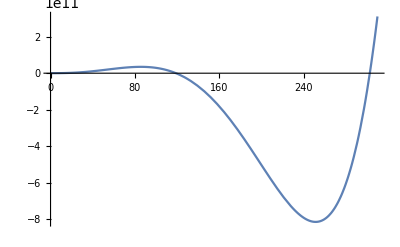

```mathematica
Plot[bistablePolSets[[14]],{Subscript[x, 1],0,310},PlotRange->Full]
```

## Test

```mathematica
pars=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],13]]*1000;
tots=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.0001])],3]]*1000;
```

```mathematica
subs={Subscript[k, 1]->pars[[1]],Subscript[k, 2]->pars[[2]],Subscript[k, 3]->pars[[3]],Subscript[k, 4]->pars[[4]],Subscript[k, 5]->pars[[5]],Subscript[k, 6]->pars[[6]],Subscript[k, 7]->pars[[7]],Subscript[k, 8]->pars[[8]],Subscript[k, 9]->pars[[9]],Subscript[k, 10]->pars[[10]],Subscript[k, 11]->pars[[11]],Subscript[k, 12]->pars[[12]],Subscript[k, 13]->pars[[13]],Subscript[T, 1]->tots[[1]],Subscript[T, 2]->tots[[2]],Subscript[T, 3]->tots[[3]]}
```

{k_1→0.0050108,k_2→2.13937×10^-8,k_3→84.0533,k_4→7.39693×10^-13,k_5→7.02824×10^-6,k_6→2.01154,k_7→0.00200499,k_8→139.788,k_9→277.28,k_10→0.00189982,k_11→3.95171×10^-14,k_12→24.1445,k_13→0.000961332,T_1→4.6296×10^-6,T_2→42.1547,T_3→6.50074×10^-12}

```mathematica
term=coeff1/.subs
```

1.86014×10^-7

```mathematica
term>0
```

True

```mathematica
Solve[pol==0/.subs,Subscript[x, 1]]
```

{{x_1→-69720.},{x_1→-42.1556},{x_1→-0.00140262},{x_1→-1.42528×10^-16},{x_1→2.79523×10^-17}}

```mathematica
pars
```

{109.979,245.987,0.013013,7.38085,0.00907035,0.000240539,8.2791×10^-7,0.0793657,50.8438,0.0447688,0.392116,0.183181,29.0273}

```mathematica
-Log[0.001]
```

6.90776

```mathematica
-Log[1000.]
```

-6.90776

```mathematica
pars=Exp[RandomReal[{Log[0.001],Log[1000.]},13]]
```

{0.00213335,0.0915725,7.60916,0.0594866,0.0724152,0.44353,0.0398721,0.266627,0.224569,0.04846,1.81477,0.0932097,0.00389391}

```mathematica
pars=Exp[RandomVariate[NormalDistribution[0,Log[1000.]],13]]
```

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}],{x,-6,6},Filling->Axis]
```

```mathematica
tots=RandomReal[{1,1.*10^4},3]/10^3
```

{9.15425,7.43704,8.1277}

```mathematica
tots=Exp[RandomReal[{Log[0.001],Log[10.]},3]]
```

{0.00214497,1.49576,0.144091}

```mathematica
solution=NSolve[{pol==0}/.subs,Subscript[x, 1]]
```

{{x_1→-0.13976},{x_1→-0.0570779-0.19538 ⅈ},{x_1→-0.0570779+0.19538 ⅈ},{x_1→-0.000112664},{x_1→0.0540014}}

```mathematica
solution=NSolve[{pol==0&&Subscript[x, 1]>0}/.subs,Subscript[x, 1],Reals]
```

{{x_1→0.0540014}}

```mathematica
x=1
x++
```